```mathematica
Table[SphericalPlot3D[Abs[SphericalHarmonicY[3,m,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2*π},PlotRange->All,ImageSize->Small],{m,-2,2}] (* Angular Distribution *)
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
a = 1;(* a is the Bohr Radius *)
R[n_,l_,r_,]:=√((2/(n*a))^3 Factorial[n-l-1]/(2 n (Factorial[n+l])^3)) Exp[-r/(n*a)]*((2*r)/(n*a))^l*LaguerreL[n-l-1,2*l+1,(2*r)/(n*a)]/.n->3 (* Radial PDF *)
```

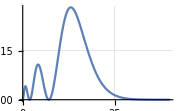
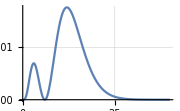
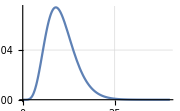

```mathematica
Table[Plot[Abs[R[3,l,r]]^2*r^2,{r,0,40},PlotRange->All,ImageSize->Small,GridLines->Automatic],{l,0,2}]
```

```mathematica
F[n_,l_,m_,r_,θ_,ϕ_]:=R[n,l,r]*SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
Table[SphericalPlot3D[Abs[F[3,l,0,1/9,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2*π},ImageSize->Medium],{l,1,2}]
```

{-Graphics3D-,-Graphics3D-}